```mathematica
Clear["`*"]
```

```mathematica
Needs["PlotLegends`"]
```

# Economics 381

## Homework

## Problem Set 1

### 1: Hands Dirty with Data

#### a.) Downloading the Data

```mathematica
SetDirectory["/Users/spencerlyon2/Documents/School/Semesters/Winter 2012/Economics 381/Homeworks/Data"];
CPILFESL =priceIndex= Import["CPILFESL.csv"];

PAYEMS =payrollEmployment= Import["PAYEMS.csv"];
GDPC96 = gdp = Import["GDPC96.csv"];
Dimensions[#]&/@{payrollEmployment,gdp,priceIndex};
```

#### b.) Plot GDP and PayrollEmp on same axis from Q1-1948 to Q3-2011

```mathematica
{payrollDate,payrollData} = Transpose[payrollEmployment[[38;;292]]];
{gdpDate,gdpData} = Transpose[gdp[[5;;259]]];
Dimensions[#]&/@{payrollData,gdpData}
```

(255
255)

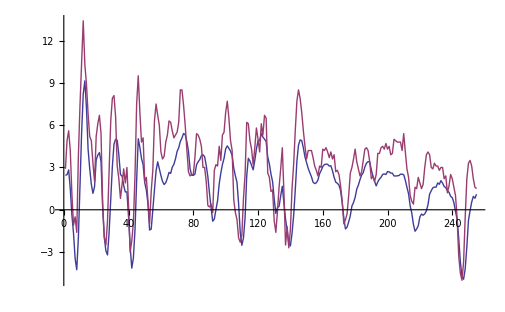

0.812196

```mathematica
ListPlot[{payrollData,gdpData},Joined->True]
Correlation[payrollData,gdpData]
```

I believe these two series are so closely related (positively) because the higher the GDP, the more goods the US produces. The more goods the US produces, the more workers it will need and the higher the employment level will be.

#### c.) Plot GDP and the CPI from Q!-1958 to Q3-2011

```mathematica
{priceDates,priceData }= Transpose[priceIndex[[6;;220]]];
newGdpData = gdpData[[40;;254]];
Dimensions[#]&/@{priceData,newGdpData}
```

(215
215)

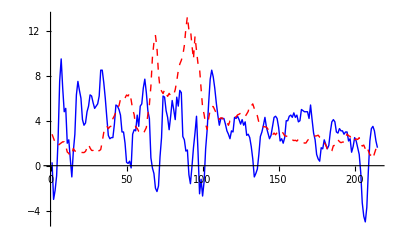

-0.198922

```mathematica
ListPlot[{newGdpData,priceData},Joined->True,GridLines->{{},{}},PlotStyle->{{Blue,Thick},{Red,Dashed}}]
Correlation[newGdpData,priceData]
```

I believe there is a somewhat weak negative relationship between GDP and the CPI because in times when GDP is high, consumption in future periods will be higher. This is due to higher average income for a US citizen in previous periods. This effect doesn’t completely take place in the same period, so a lagged effect of GPD on the CPI could explain why the relationship is weak. 

The sign of the correlation can also be explained by the same lagged idea that was spoken of before. As GDP is increasing, CPI will follow and increase in later periods. When GPD stops increasing as much ( negative second derivative) the CPI is still rising because of increased income in previous periods. This results in the direction of change in the two statistics to be in the opposite direction much of the time.

Both of these ideas can be seen clearly in the graph above.

### 2.) Problems and Applications: Chapter 2, #6: S A farmer grows a bushel of wheat and sells it to a miller for $1.00. The Miller turns the wheat into flour and then sell the flour to a Baker for $3.00. The baker uses the flour to make bread and sells the bread to an engineer for $6.00. The engineer eats the bread. What is the value added by each person? What is GDP?

### 3.) Chapter 2, Related employment Question: Suppose an economy is made up of 100 people who are in the following mutually exclusive categories shown in Table 1. Three concepts are at play here: adult population, workforce, and labor force. A simple definition of the workforce is everybody in the economy who is 16 or older. So the labor force is a subset of the workforce, and the workforce is a subset of the adult population.

#### (a) What is the percent of the adult population not in the labor force?

#### (b) What is the labor force participation rate?

#### (c) What is the unemployment rate?

## Problem Set 2

### 3.3 in text: Suppose that an economy’s production function is Cobb-Douglass with parameter α = 0.3 a.) What fractions of Income do capital and labor receive? b.) Suppose the immigration increases the labor force by 10%. What happens to total output, in percent? The rental price of capital? The real wage? c.) Suppose that a gift of capital from abroad raises the capital stock by 10%. What happens to total output, in percent? The rental price of capital? The real wage? d.) Suppose that a technological advance raises the value of the parameter A by 10%. What happens to total output, in percent? The rental price of capital? The real wage?

### 3.6 in text: Consider a Cobb-Douglas production function with three inputs. K is capital (# of machines), L is labor (# of workers), and H is human capital (# of college degrees among workers). The production function is Y = K^(1/3)L^(1/3)H^(1/3). a.) Derive an expression for the marginal product of labor. How does an increase in the amount of human capital affect the marginal product of labor? b.) Derive an expression for the marginal product of human capital. How does an increase in the amount of human capital affect the marginal product of human capital? c.) what is the income share paid to labor? What is the income share paid to capital? In the national income account of this economy, what share of total income do you think workers would appear to receive? (Hint: Consider where the return to human capital shows up.) d.) An unskilled worker earns the marginal product of labor, whereas a skilled worker earns the marginal product of labor plus the marginal product of human capital. Using your answers to (a) and (b), find the ratio of skilled wage to the unskilled wage. How does an increase in the amount of human capital affect this ratio? Explain. e.) Some people advocate government funding of college scholarships as a way of creating a more egalitarian society. Others argue that scholarships help only those who are able to go to college. Do your answers to the preceding questions shed light on the debate?

### 3.9 in text: Consider an economy described by the following equations: Y = C + I + G Y = 5,000 G = 1,000 T = 1,000 C = 250 + 0.75(Y - T) I = 1,000 -50r a.) In this economy, compute private saving, public saving, and national saving. b.) Find the equilibrium interest rate. c.) Now suppose that G rises to 1,250. Compute private saving, public saving, and national saving. d.) Find the new equilibrium interest rate.

### 3.10 in text: Suppose that the government increases taxes and government purchases by equal amounts. What happens to the interest rate and investment in response to this balanced-budget change? Does your answer depend on the marginal propensity to consume?

### Hands Dirty with Data: In this problem, you will retrieve and manipulate macroeconomic data and verify some relationships that inform mactoeconomic theory.

#### a.) Go the Federal Reserve Bank of St. Louis’ Federal Reserve Economic Data (FRED) website at http://research.stlouisfed.org/fred2/ and down- load the following two data series into an Excel file. You can then do the subsequent analysis using either Excel or Stata: Consumer Price Index for All Urban Consumers (CPILFESL), all items less food and energy, year over year percentage change. Make sure you set the units of account to “percent change from year ago” on the download page. M1 Money Stock (M1SL), percent change from year ago. Make sure you set the units of account to “percent change from year ago” on the download page.

```mathematica
SetDirectory["/Users/spencerlyon2/Documents/School/Semesters/Winter 2012/Economics 381/Homeworks/Data"];
CPILFESL2 = Transpose[Import["CPILFESL2.csv"]][[2]];
M1SL = Transpose[ Import["M1SL.csv"]][[2]];
```

#### b.) Create a chart that plots both the CPI (% chg. from year ago) and M1 Money Stock (% chg. from year ago) from 1960M1 to 2011M11. Calculate the correlation of the two series over the period 1960M1 to 2011M11.

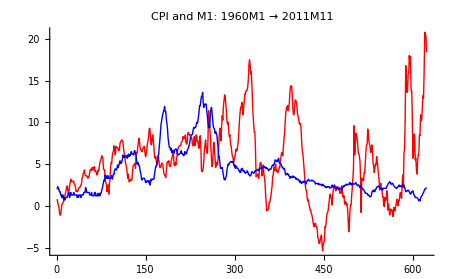

```mathematica
ListPlot[{M1SL,CPILFESL2},Joined->True,PlotStyle->{{Red},{Blue}},PlotLabel->"CPI and M1: 1960M1 → 2011M11"]
```

```mathematica
Correlation[M1SL,CPILFESL2]
```

0.171266

#### c.) Now create a 10-year average CPI annual growth rate by putting a formula in each cell starting in 1967M12 that averages the past 120 months of annual growth rates.3 Create the same10-year average annual growth rate series for M1 Money Stock but starting in 1969M12. Create a chart that plots both the 10-year average annual CPI growth rate and the 10-year average annual M1 Money Stock growth rate from 1969M12 to 2011M11. Calculate the correlation of the two series over the period 1969M12 to 2011M11. How do you explain the difference in the correlations between part (a) and part(b)? (Hint: Has to do with short-term and long-term.)

```mathematica
cpiaverage = Transpose[Import["CPILFESL (1).csv"]][[3]]; cpilength = Length[cpiaverage]; cpiPlot = cpiaverage[[144;;cpilength]];
M1SL = Transpose[Import["M1SL (1).csv"]][[3]]; M1SLlength = Length[M1SL]; M1SLplot = M1SL[[120;;M1SLlength]];
```

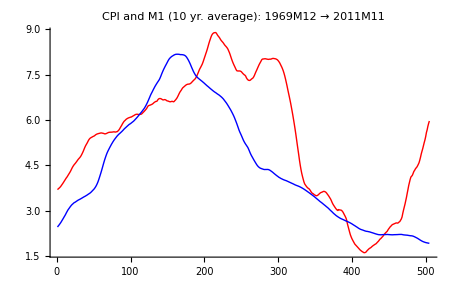

```mathematica
ListPlot[{M1SLplot,cpiPlot},Joined->True,PlotStyle->{{Red},{Blue}},PlotLabel->"CPI and M1 (10 yr. average): 1969M12 → 2011M11"]
```

```mathematica
Correlation[M1SLplot,cpiPlot]
```

0.770171

The long term correlation is much higher than that of the short term because in the short term the money supply is relatively fixed. The fed only has so much power to change the money supply and those methods all take time for their full effects to be felt. If you broaden the scope of your time frame you will see that the money supply and prices move together fairly well. In the short term, the volatility of prices simply cannot be matched by a change in the money supply.

## Problem Set 3

### 1.) Assume that real output is .0cxed at .16 Y = 300, consumption is .0cxed at .16 C = 200, government spending is .0cxed at .16G = 30. Assume that the Investment function takes the following form I(r) = 75:dbc0:dc00r, where r is given in percent terms (i.e., r = 2 signi.0ces an interest rate of 2%). Assume that the quantity equation of money holds M .01 V = P .01 Y and the velocity of money is constant .16 V .

#### a.) If the money supply increases by %3, by what percentage rate do prices change? That is, what is the inflation rate? b.) What is the real rate of investment r in this economy? What is the investment level I? c.) ) What is the nominal interest rate i?

#### d.) If government spending G increases to 35, what happens to the real rate of investment r, investment I, and the nominal interest rate i?

### Problem (#2 in text) Consider an economy described by the following equations: Y = C + I + G + NX, Y = 5,000, G = 1,000, T = 1,000, C = 250 + 0.75( Y - T ), I = 1,000 - 50r, NX = 500 - 500e, r = r* = 5. a.

#### a.) In this economy, solve for national saving, investment, the trade balance, and the equilib-rium exchange rate.

#### b.) Suppose now that G rises to 1,250. Solve for national saving, investment, the trade balance, and the equilibrium exchange rate. Explain what you find.

#### c.) Now suppose that the world interest rate rises from 5 to 10 percent. ( G is again 1,000) Solve for national saving, investment, the trade balance, and the equilibrium exchange rate. Explain what you find.

### Problem 3 (#7 in text) The president is considering placing a tariff on the import of Japanese luxury cars. Discuss the economics and politics of such a policy. In par-ticular, how would the policy affect the U. S. trade deficit? How would it affect the exchange rate? Who would be hurt by such a policy? Who would benefit?

### Problem 4 (# 11 in text) You read in a newspaper that the nominal interest rate is 12 percent per year in Canada and 8 percent per year in the United States. Suppose that the real interest rates are equalized in the two countries and that purchasing- power parity holds.

#### a.) Using the Fisher equation ( discussed in Chapter 4), what can you infer about expected inflation in Canada and in the United States?

#### b.) What can you infer about the expected change in the exchange rate between the Canadian dollar and the U. S. dollar?

#### c.) A friend proposes a get- rich- quick scheme: borrow from a U. S. bank at 8 percent, deposit the money in a Canadian bank at 12 percent, and make a 4 percent profit. What’s wrong with this scheme?

## Problem Set 4

### 7.1: Country A and country B both have the production function Y = F( K, L) = K^(1/2)L^(1/2).

#### a. Does this production function have constant returns to scale? Explain.

#### b. What is the perworker production function, y = f( k)?

#### c. Assume that neither country experiences population growth or technological progress and that 5 percent of capital depreciates each year. Assume further that country A saves 10 percent of output each year and country B saves 20 percent of output each year. Using your answer from part ( b) and the steady-state condition that investment equals depreciation, find the steady-state level of capital per work-er for each country. Then find the steady- state levels of income per worker and consumption per worker.

#### d. Suppose that both countries start off with a capital stock per worker of 2. What are the levels of income per worker and consumption per worker? Remembering that the change in the capital stock is investment less depreciation, use a calculator or a computer spreadsheet to show how the capital stock per worker will evolve over time in both countries. For each year, calculate income per worker and consumption per worker. How many years will it be before the consumption in country B is higher than the consumption in country A?

### 7.3: Consider an economy described by the produc-tion function: Y = F( K, L) = K^0.3 L^0.7

#### a. What is the per- worker production function?

#### b. Assuming no population growth or technological progress, find the steady-state capital stock per worker, output per worker, and consumption per worker as a function of the saving rate and the depreciation rate.

#### c. Assume that the depreciation rate is 10 percent per year. Make a table showing steady- state capital per worker, output per worker, and consumption per worker for sav-ing rates of 0 percent, 10 percent, 20 percent, 30 percent, and so on. ( You will need a calcu-lator with an exponent key for this.) What saving rate maximizes output per worker? What saving rate maximizes consumption per worker?

#### d. ( Harder) Use calculus to find the marginal product of capital. Add to your table the marginal product of capital net of depreciation for each of the saving rates. What does your table show?

### 7.7: In the Solow model, population growth leads to steady- state growth in total output, but not in output per worker. Do you think this would still be true if the production function exhibited increasing or decreasing returns to scale? Explain. ( For the definitions of increasing and decreasing returns to scale, see Chapter 3, “ Prob-lems and Applications,” Problem 2.)

### 8.2: In the United States, the capital share of GDP is about 30 percent, the average growth in output is about 3 percent per year, the deprecia-tion rate is about 4 percent per year, and the capital– output ratio is about 2.5. Suppose that the production function is Cobb– Douglas, so that the capital share in output is constant, and that the United States has been in a steady state. ( For a discussion of the Cobb– Douglas produc-tion function, see Chapter 3.)

#### a. What must the saving rate be in the initial steady state? [ Hint: Use the steady- state rela-tionship, sy = ( d + n + g) k.]

#### b. What is the marginal product of capital in the initial steady state?

#### c. Suppose that public policy raises the saving rate so that the economy reaches the Golden Rule level of capital. What will the marginal product of capital be at the Golden Rule steady state? Compare the marginal product at the Golden Rule steady state to the marginal product in the initial steady state. Explain.

#### d. What will the capital– output ratio be at the Golden Rule steady state? ( Hint: For the Cobb– Douglas production function, the capital– output ratio is related to the marginal product of capital.)

### 8.4: Two countries, Richland and Poorland, are described by the Solow growth model. They have the same Cobb– Douglas production function, F( K, L) = A KaL1- a, but with different quantities of capital and labor. Richland saves 32 percent of its income, while Poorland saves 10 percent. Richland has population growth of 1 percent per year, while Poorland has population growth of 3 percent. ( The numbers in this problem are chosen to be approximately realistic descriptions of rich and poor nations.) Both nations have technologi-cal progress at a rate of 2 percent per year and depreciation at a rate of 5 percent per year.

#### a. What is the per- worker production function f( k)?

#### b. Solve for the ratio of Richland’s steady- state income per worker to Poorland’s. ( Hint: The parameter a will play a role in your answer.)

#### c. If the Cobb– Douglas parameter a takes the conventional value of about 1/ 3, how much higher should income per worker be in Richland compared to Poorland?

#### d. Income per worker in Richland is actually 16 times income per worker in Poorland. Can you explain this fact by changing the value of the parameter a? What must it be? Can you think of any way of justifying such a value for this parameter? How else might you explain the large difference in income between Richland and Poorland?

```mathematica
.2/0.05
```

4.

```mathematica
.9*2
```

1.8

```mathematica
.8*4
```

3.2

```mathematica
Solve[s/d==k^(.7),k]
```

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k→1. (s/d)^1.42857142857143}}

```mathematica
10/7.
```

1.42857

```mathematica
(x^(10/7))^(3/10)//Simplify
```

(x^(10/7))^(3/10)

```mathematica
D[k^0.3,k]
```

0.3/k^0.7

```mathematica
.32/.08
```

4.

## Problem Set 6

```mathematica
Manipulate[GraphicsGrid[{{Null,Plot[x+s,{x,-5,5},PlotRange->{-5,5}],Null},

{Plot[2x,{x,-5,5}],Plot[-x+3,{x,-5,5}],Plot[3,{x,-5,5}]},

{Null,Plot[1.5x,{x,-5,5}]}}],

{s,-2,2}]
```

```mathematica
DynamicModule
```

## Problem Set 8

### 19.1

```mathematica
ms[cr_,rr_,B_]:=B*((cr+1)/(cr+rr))
```

```mathematica
ms[.17,.14,7.1]
ms[.41,.21,8.4]
```

26.7968

19.1032

#### a.)

```mathematica
ms[.17,.14,7.1]
 ms[.41,.14,8.4]
ms[.17,.14,7.1]- ms[.41,.14,8.4]
```

26.7968

21.5345

5.26223

#### b.)

```mathematica
ms[.17,.14,7.1]
ms[.17,.21,8.4]
ms[.17,.14,7.1]-ms[.17,.21,8.4]
```

26.7968

25.8632

0.933616

### 17.2

```mathematica
110/100.
```

1.1

## Daily Reviews

### Solow Growth Model, Steady State Capital Stock Problem

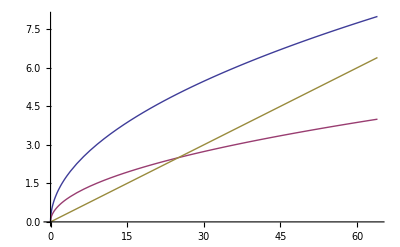

ReplaceAll::reps: {{x → 25} == √x/2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::naqs: x/. {x → 25} == √x/2 is not a quantified system of equations and inequalities.

Solve[x/.{x→25}==(√x)/2,x]

```mathematica
Plot[{√x,1/2 √x,1/10x},{x,0,64},PlotLegend->{"y = f(k)","i = sf(k)","δk"},LegendPosition->{0.8,-0.8},GridLines->{{x/.Solve[1/10*x==1/2 √x,x][[2]]},{5/2,5}}]
```

k_(t+1) = K_t + i_t +-δk_t